## advection1_spherical (general solution)

{True}

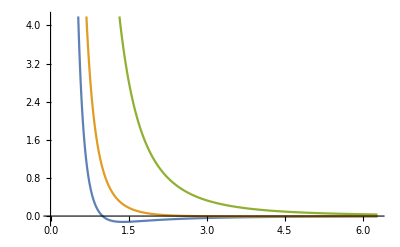

```mathematica
ClearAll["Global`*"];
eq=D[f[r,t],t]==-1/r^2 D[r^2 v r f[r,t],r];
sol = DSolve[eq,f,{r,t}];
ff[r_,t_]=f[r,t]/.sol[[1]]/.{C[1][t_]->t};
FullSimplify[eq/.sol/.{C[1][t_]->t}]
v=1;
Plot[{ff[r,0],ff[r,1],ff[r,10]},{r,0,2 Pi}]
```

## advection1_spherical (particular solution)

{{f→Function[{r,t},ⅇ^(-3 t v) Cos[ⅇ^(-t v) r]]}}

ⅇ^(-3 t v) Cos[ⅇ^(-t v) r]

{True}

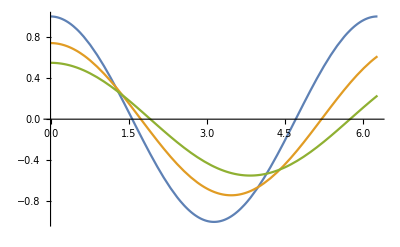

0

```mathematica
ClearAll["Global`*"];
eq=D[f[r,t],t]==-1/r^2 D[r^2 v r f[r,t],r];
sol = DSolve[{eq,f[r,0]==Cos[r]},f,{r,t}]
ff[r_,t_]=f[r,t]/.sol[[1]]
FullSimplify[eq/.sol]
v=1;
Plot[{ff[r,0],ff[r,0.1],ff[r,.2]},{r,0,2 Pi}]
(*also test if weak form accepts the above analyic soltion*)
w=Sin[r]; (*some random test function in the finite element sense*)
p=v r; (*flux*)
FullSimplify[Integrate[w r^2D[ff[r,t],t],r]-Integrate[p r^2 ff[r,t] D[w,r],r]+w p r^2 ff[r,t]](*this == 0, so yeah it works *)
```